This is the third of three notebooks which accompany the paper “Gravitational Waves on Kerr Black Holes I: Reconstruction of Linearized Metric Perturbations” https://arxiv.org/abs/2403.20311. This notebook imports the results of Metric Perturbation.nb and shows how to plot a tetrad or coordinate component of the metric perturbation. This notebook uses the SpinWeightedSpheroidalHarmonics package from the BHPToolkit, which can be installed from here: https://bhptoolkit.org/SpinWeightedSpheroidalHarmonics/.

## 1. Setup and Definitions

We call the SpinWeightedSpheroidalHarmonics package, allow subscripts on our variables, and set the working directory to this notebook’s path.

```mathematica
<<SpinWeightedSpheroidalHarmonics`
<<Notation`
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]
SetDirectory@NotebookDirectory[];
```

We define various useful symbols, as well as the metric and tetrad vectors in Boyer-Lindquist coordinates.

```mathematica
$Assumptions = {
0 < a < M, 
0 <M+Sqrt[M^2-a^2]< r, 
Element[θ, Reals], 
Element[t, Reals], 
Element[ϕ, Reals],
Element[m,Integers],
Element[s,Reals]
};

coord={t,r,θ,ϕ};

Δ=r^2-2M*r+a^2;
Σ=r^2+a^2*Cos[θ]^2;
ζ=r-I*a*Cos[θ];
ζbar=r+I*a*Cos[θ];
ωsub={Conjugate[ω]->ωbar,Conjugate[ωbar]->ω};
K[ω_,m_]:=(r^2+a^2)*ω-a*m;
Kbar[ω_,m_]:=(r^2+a^2)*Conjugate[ω]-a*m/.ωsub;
Q[ω_,m_]:=-a*ω*Sin[θ]+m*Csc[θ];
Qbar[ω_,m_]:=-a*Conjugate[ω]*Sin[θ]+m*Csc[θ]/.ωsub;
gBL=-ϵg*{{(1-(2M*r)/Σ),0,0,(a*Sin[θ]^2*(2M*r))/Σ},{0,-Σ/Δ,0,0},{0,0,-Σ,0},{(a*Sin[θ]^2*(2M*r))/Σ,0,0,-(((r^2+a^2)^2-Δ*a^2*Sin[θ]^2)/Σ)*Sin[θ]^2}};
lupBL = {(r^2+a^2)/Δ,1,0,a/Δ};
nupBL = 1/(2*Σ)*{r^2+a^2,-Δ,0,a}; 
mupBL = 1/(Sqrt[2]*ζbar)*{I*a*Sin[θ],0,1,I/Sin[θ]}; 
mbarupBL = 1/(Sqrt[2]*ζ)*{-I*a*Sin[θ],0,1,-I/Sin[θ]};
ldownBL=gBL.lupBL//Simplify;
ndownBL=gBL.nupBL//Simplify;
mdownBL=gBL.mupBL//Simplify;
mbardownBL=gBL.mbarupBL//Simplify;
```

## 2. Radial and Angular Mode Functions

We define the radial and angular Teukolsky equations.

```mathematica
eqR=Δ^-s*D[Δ^(s+1)*D[R[s,ω,l,m,r],r],r]+((K[ω,m]^2-2*I*s*(r-M)*K[ω,m])/Δ+4*I*s*ω*r-λ[s,ω,l,m])*R[s,ω,l,m,r];
eqS=-Sin[θ]^-1*D[Sin[θ]^2*(-Sin[θ]^-1*D[S[s,ω,l,m,θ],θ]),θ]+(a^2*ω^2*Cos[θ]^2-(m+s*Cos[θ])^2/Sin[θ]^2-2*a*s*ω*Cos[θ]+s+A)*S[s,ω,l,m,θ]/.A->λ[s,ω,l,m]+2*a*m*ω-a^2*ω^2;
eqRbar=Δ^-s*D[Δ^(s+1)*D[Rbar[s,ω,l,m,r],r],r]+((Kbar[ω,m]^2+2*I*s*(r-M)*Kbar[ω,m])/Δ-4*I*s*ωbar*r-λbar[s,ω,l,m])*Rbar[s,ω,l,m,r];
eqSbar=-Sin[θ]^-1*D[Sin[θ]^2*(-Sin[θ]^-1*D[Sbar[s,ω,l,m,θ],θ]),θ]+(a^2*ωbar^2*Cos[θ]^2-(m+s*Cos[θ])^2/Sin[θ]^2-2*a*s*ωbar*Cos[θ]+s+A)*Sbar[s,ω,l,m,θ]/.A->λbar[s,ω,l,m]+2*a*m*ωbar-a^2*ωbar^2;
```

Using the above equations of motion, we define rules to remove second radial and angular derivatives of the mode functions. We then check that these rules yield zero when applied to the equations of motion.

```mathematica
Rsub={D[R[s0_,ω0_,l0_,m0_,r],{r,2}]:>Evaluate[Simplify[D[R[s,ω,l,m,r],{r,2}]/.Solve[eqR==0,D[R[s,ω,l,m,r],{r,2}]]][[1]]]/.{s->s0,ω->ω0,ωbar->Conjugate[ω0],l->l0,m->m0},D[Rbar[s0_,ω0_,l0_,m0_,r],{r,2}]:>Evaluate[Simplify[D[Rbar[s,ω,l,m,r],{r,2}]/.Solve[eqRbar==0,D[Rbar[s,ω,l,m,r],{r,2}]]][[1]]]/.{s->s0,ω->ω0,ωbar->Conjugate[ω0],m->m0}};
Ssub={D[S[s0_,ω0_,l0_,m0_,θ],{θ,2}]:>Evaluate[Simplify[D[S[s,ω,l,m,θ],{θ,2}]/.Solve[eqS==0,D[S[s,ω,l,m,θ],{θ,2}]]][[1]]]/.{s->s0,ω->ω0,ωbar->Conjugate[ω0],l->l0,m->m0},D[Sbar[s0_,ω0_,l0_,m0_,θ],{θ,2}]:>Evaluate[Simplify[D[Sbar[s,ω,l,m,θ],{θ,2}]/.Solve[eqSbar==0,D[Sbar[s,ω,l,m,θ],{θ,2}]]][[1]]]/.{s->s0,ω->ω0,ωbar->Conjugate[ω0],m->m0}};
```

```mathematica
{eqR==0,eqRbar==0}/.Rsub/.ωsub//Simplify
{eqS==0,eqSbar==0}/.Ssub/.ωsub//Simplify
```

{True,True}

{True,True}

## 3. Radial and Angular Modes in Terms of Heun Functions

Subscripted definitions have to be done outside of the initialization blocks .

```mathematica
SubPlus[r]=M+√(M^2-a^2);
SubMinus[r]=M-√(M^2-a^2);
SubPlus[c]=(2 M SubPlus[r])/(SubPlus[r]-SubMinus[r]);
SubMinus[c]=(2 M SubMinus[r])/(SubPlus[r]-SubMinus[r]);
SubPlus[Ω]=a/(2 M SubPlus[r]);
SubMinus[Ω]=a/(2 M SubMinus[r]);
```

### Angular Modes

We define explicit solutions to the angular Teukolsky equation in terms of confluent Heun functions. The normalization matches that of Eq. (2.6).

```mathematica
Shat[s_,ω_,l_,m_,θ_]:=Module[{μ1,μ2,β,p},
μ1=Abs[s+m]/2;
μ2=Abs[s-m]/2;
β=2*a*ω*(μ1+μ2+s+1);
p=-λ[s,ω,l,m]-2*m*a*ω+2*a*ω*(μ1-μ2)+(μ1+μ2)^2+μ1+μ2-s*(s+1);
(1-Cos[θ])^μ1(1+Cos[θ])^μ2 Exp[a*ω*(1+Cos[θ])]HeunC[-p+β,2*β,2*μ2+1,2*μ1+1,4*a*ω,(1+Cos[θ])/2]
];
Shatbar[s_,ω_,l_,m_,θ_]:=Module[{μ1,μ2,β,p},
μ1=Abs[s+m]/2;
μ2=Abs[s-m]/2;
βbar=2*a*Conjugate[ω]*(μ1+μ2+s+1);
pbar=-λbar[s,ω,l,m]-2*m*a*Conjugate[ω]+2*a*Conjugate[ω]*(μ1-μ2)+(μ1+μ2)^2+μ1+μ2-s*(s+1);
(1-Cos[θ])^μ1(1+Cos[θ])^μ2 Exp[a*Conjugate[ω]*(1+Cos[θ])]HeunC[-pbar+βbar,2*βbar,2*μ2+1,2*μ1+1,4*a*Conjugate[ω],(1+Cos[θ])/2]
];
```

We check that these functions are in fact solutions.

```mathematica
eqS==0/.{S->Function[{s,ω,l,m,θ},Shat[s,ω,l,m,θ]]} //FullSimplify
eqSbar==0/.{Sbar->Function[{s,ω,l,m,θ},Shatbar[s,ω,l,m,θ]]}/.ωsub //FullSimplify
```

True

True

### Radial Modes

We define explicit solutions to the radial Teukolsky equation in terms of confluent Heun functions. The normalization matches that of Eq. (2.17).

```mathematica
Rhatin[s_,ω_,l_,m_,r_]:=Module[{ξ1,ξ2,γ,δ,ϵ,α,q},
γ=2ξ1+s+1;
δ=2ξ2+s+1;
ϵ=-2 ⅈ ω(SubPlus[r]-SubMinus[r]);
α=-2 ⅈ ω(2s+1)(SubPlus[r]-SubMinus[r]);
q=-2ⅈ ω SubPlus[r](2s+1)+λ[s,ω,l,m];
ξ1=ⅈ SubPlus[c](ω-m SubPlus[Ω]);
ξ2=-ⅈ SubMinus[c](ω-m SubMinus[Ω]);
(SubPlus[r]-SubMinus[r])^(-ξ2-s)(r-SubPlus[r])^(-ξ1-s)(r-SubMinus[r])^ξ2 Exp[ⅈ ω (r-SubPlus[r])]HeunC[q+(ϵ-δ)(1-γ),α+ϵ(1-γ),2-γ,δ,ϵ,-(r-SubPlus[r])/(SubPlus[r]-SubMinus[r])]
];
Rhatout[s_,ω_,l_,m_,r_]:=Module[{ξ1,ξ2,γ,δ,ϵ,α,q},
γ=2ξ1+s+1;
δ=2ξ2+s+1;
ϵ=-2 ⅈ ω(SubPlus[r]-SubMinus[r]);
α=-2 ⅈ ω(2s+1)(SubPlus[r]-SubMinus[r]);
q=-2ⅈ ω SubPlus[r](2s+1)+λ[s,ω,l,m];
ξ1=ⅈ SubPlus[c](ω-m SubPlus[Ω]);
ξ2=-ⅈ SubMinus[c](ω-m SubMinus[Ω]);
(SubPlus[r]-SubMinus[r])^-ξ2(r-SubPlus[r])^ξ1(r-SubMinus[r])^ξ2 Exp[ⅈ ω(r-SubPlus[r])]HeunC[q,α,γ,δ,ϵ,-(r-SubPlus[r])/(SubPlus[r]-SubMinus[r])]
];
Rhatbarin[s_,ω_,l_,m_,r_]:=Module[{ξ1bar,ξ2bar,γbar,δbar,ϵbar,αbar,qbar},
γbar=2ξ1bar+s+1;
δbar=2ξ2bar+s+1;
ϵbar=2 ⅈ Conjugate[ω](SubPlus[r]-SubMinus[r]);
αbar=2 ⅈ Conjugate[ω](2s+1)(SubPlus[r]-SubMinus[r]);
qbar=2ⅈ Conjugate[ω] SubPlus[r](2s+1)+λbar[s,ω,l,m];
ξ1bar=-ⅈ SubPlus[c](Conjugate[ω]-m SubPlus[Ω]);
ξ2bar=ⅈ SubMinus[c](Conjugate[ω]-m SubMinus[Ω]);
(SubPlus[r]-SubMinus[r])^(-ξ2bar-s)(r-SubPlus[r])^(-ξ1bar-s)(r-SubMinus[r])^ξ2bar Exp[-ⅈ Conjugate[ω] (r-SubPlus[r])]HeunC[qbar+(ϵbar-δbar)(1-γbar),αbar+ϵbar(1-γbar),2-γbar,δbar,ϵbar,-(r-SubPlus[r])/(SubPlus[r]-SubMinus[r])]
];
Rhatbarout[s_,ω_,l_,m_,r_]:=Module[{ξ1bar,ξ2bar,γbar,δbar,ϵbar,αbar,qbar},
γbar=2ξ1bar+s+1;
δbar=2ξ2bar+s+1;
ϵbar=2 ⅈ Conjugate[ω](SubPlus[r]-SubMinus[r]);
αbar=2 ⅈ Conjugate[ω](2s+1)(SubPlus[r]-SubMinus[r]);
qbar=2ⅈ Conjugate[ω] SubPlus[r](2s+1)+λbar[s,ω,l,m];
ξ1bar=-ⅈ SubPlus[c](Conjugate[ω]-m SubPlus[Ω]);
ξ2bar=ⅈ SubMinus[c](Conjugate[ω]-m SubMinus[Ω]);
(SubPlus[r]-SubMinus[r])^-ξ2bar(r-SubPlus[r])^ξ1bar(r-SubMinus[r])^ξ2bar Exp[-ⅈ Conjugate[ω](r-SubPlus[r])]HeunC[qbar,αbar,γbar,δbar,ϵbar,-(r-SubPlus[r])/(SubPlus[r]-SubMinus[r])]
];
```

We check that these functions are in fact solutions.

```mathematica
eqR==0/.{R->Function[{s,ω,l,m,r},Rhatin[s,ω,l,m,r]]} //FullSimplify
eqR==0/.{R->Function[{s,ω,l,m,r},Rhatout[s,ω,l,m,r]]} //FullSimplify
eqRbar==0/.{Rbar->Function[{s,ω,l,m,r},Rhatbarin[s,ω,l,m,r]]} /.ωsub//FullSimplify
eqRbar==0/.{Rbar->Function[{s,ω,l,m,r},Rhatbarout[s,ω,l,m,r]]}/.ωsub //FullSimplify
```

True

True

True

«1 more identical outputs»

## 4. Plotting Metric Perturbation Example

We import the tetrad components in IRG.

```mathematica
<<"./metric-perturbations/habIRG.mx"
```

```mathematica
complexSub={A->Subscript[A, x]+ⅈ Subscript[A, y],Abar->Subscript[A, x]-ⅈ Subscript[A, y],B->Subscript[B, x]+ⅈ Subscript[B, y],Bbar->Subscript[B, x]-ⅈ Subscript[B, y],ω->Subscript[ω, x]+ⅈ Subscript[ω, y],ωbar->Subscript[ω, x]-ⅈ Subscript[ω, y]};
modeSub ={
S->Function[{s,ω,l,m,θ},Shat[s,ω,l,m,θ]],
Sbar->Function[{s,ω,l,m,θ},Shatbar[s,ω,l,m,θ]],
R->Function[{s,ω,l,m,r},Rhatin[s,ω,l,m,r]],
Rbar->Function[{s,ω,l,m,r},Rhatbarin[s,ω,l,m,r]]
};
```

```mathematica
SubStar[a]=1/10;
SubStar[M]=1;
SubStar[l]=3;
SubStar[m]=0;
Subscript[ω, xstar]=1/3;
Subscript[ω, ystar]=0;
hnn=habIRG[[2,2]];
%/.complexSub/.modeSub;
%/.{λ->Function[{s,ω,l,m},SpinWeightedSpheroidalEigenvalue[s,l,m,SubStar[a] ω]],λbar->Function[{s,ω,l,m},Conjugate[SpinWeightedSpheroidalEigenvalue[s,l,m,SubStar[a] ω]]]};
%/.{Subscript[A, x]->1,Subscript[A, y]->0,Subscript[B, x]->0,Subscript[B, y]->0,M->SubStar[M],a->SubStar[a],m->SubStar[m],ϵg->1,l->SubStar[l],Subscript[ω, x]->Subscript[ω, xstar],Subscript[ω, y]->Subscript[ω, ystar],ϕ->0.5,t->1.2,θ->Pi/4};
hnnforplot=%;
```

{-0.0198248,-0.110297,-0.284106,-0.551439,-0.921615,-1.40245,-1.99986,-2.7177,-3.55756,-4.51874,-5.59821,-6.79059,-8.08816,-9.48094,-10.9567,-12.5012,-14.098,-15.729,-17.3743,-19.0123,-20.6202,-22.1741,-23.649,-25.0191,-26.2584,-27.3405,-28.2388,-28.9272,-29.3802,-29.5726,-29.4808,-29.0821,-28.3553,-27.281,-25.8419,-24.0228,-21.8107,-19.1953,-16.1693,-12.7277}

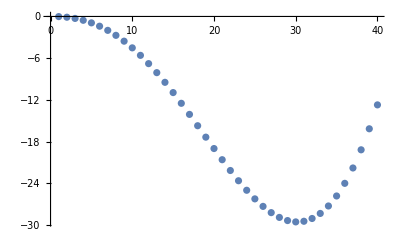

```mathematica
rmin=1.1*SubPlus[r]/.{a->SubStar[a],M->SubStar[M]};
rmax=5*SubPlus[r]/.{a->SubStar[a],M->SubStar[M]};
Δr=1*SubPlus[r]/.{a->SubStar[a],M->SubStar[M]};
Table[hnnforplot//Chop,{r,rmin,rmax,Δr}]
ListPlot[%]
```

## 5. Metric Perturbations for Single Modes of Weyl Scalars

As shown in sections 2.7 and 2.8 of the paper, one can choose the  and  coefficients so that the metric perturbation corresponds to a single mode in either of the Weyl scalars  and . These coefficients depend on the radial and angular Teukolsky-Starobinsky constants defined in section 2.4 of the paper.

```mathematica
calD[ω_,l_,m_]:=Module[{Subscript[λ, +2],t1,t2,t3},
Subscript[λ, +2]=λ[2,ω,l,m];
t1=(Subscript[λ, +2]+4)^2(Subscript[λ, +2]+6)^2;
t2=8 a ω (m - a ω)(Subscript[λ, +2]+4)(5 Subscript[λ, +2]+26);
t3=48 (a ω)^2(2 Subscript[λ, +2]+8+3(m - a ω)^2);
t1+t2+t3
]
calC[ω_,l_,m_]:=calD[ω,l,m]+(12 ω M)^2;

(* Angular constants *)
p1[ω_,x_]:=x+6 a ω+4;
p2[ω_,x_]:=x^2+2(4 a ω+5)x+4(3 (a ω)^2+8 a ω+6);
p3[ω_,x_]:=x^3-2(3 a ω-8)x^2-4((a ω)^2+8 a ω-21)x+8(3(a ω)^3-8(a ω)^2-a ω+18);
Dhat[ω_,l_,m_]:=Module[{Subscript[λ, +2]},
Subscript[λ, +2]=λ[2,ω,l,m];
Which[
m>=2,((m-2)!)/((m+2)!)calD[ω,l,m],
m==1,-1/6 p3[ω,Subscript[λ, +2]],
m==0,p2[-ω,Subscript[λ, +2]],
m==-1,-6p1[-ω,Subscript[λ, +2]],
m<=-2,((m+1)!)/((m-3)!)
]
]
DhatPrime[ω_,l_,m_]:=Module[{Subscript[λ, +2]},
Subscript[λ, +2]=λ[2,ω,l,m];
Which[
m>=2,((m+2)!)/((m-2)!),
m==1,-6p1[ω,Subscript[λ, +2]],
m==0,p2[ω,Subscript[λ, +2]],
m==-1,-1/6 p3[-ω,Subscript[λ, +2]],
m<=-2,((m-3)!)/((m+1)!)calD[ω,l,m]
]
];

(* Radial constants *)
Γ[ω_,m_]:=Module[{σ2,w},
σ2=SubPlus[r]-SubMinus[r];
w=4 M (ω-m SubPlus[Ω])SubPlus[r];
(w+2 ⅈ σ2)(w+ⅈ σ2)w(w-ⅈ σ2)
]
Γ̃[ω_,m_]:=Module[{σ2,w},
σ2=SubPlus[r]-SubMinus[r];
w=4 M (ω-m SubPlus[Ω])SubPlus[r];
(w-2 ⅈ σ2)(w-ⅈ σ2)w(w+ⅈ σ2)
]
𝒞in[ω_,l_,m_]:=Γ[ω,m];
𝒞inPrime[ω_,l_,m_]:=calC[ω,l,m]/Γ[ω,m];
𝒞out[ω_,l_,m_]:=calC[ω,l,m]/Γ̃[ω,m];
𝒞outPrime[ω_,l_,m_]:=Γ̃[ω,m];
```

We define four rules for a single mode of  in IRG/ORG, and a single mode of  in IRG/ORG, respectively.

```mathematica
IRGWeyl0={A->X,Abar->X,B->X,Bbar->X};
ORGWeyl0={A->X,Abar->X,B->X,Bbar->X};
IRGWeyl4={A->X,Abar->X,B->X,Bbar->X};
ORGWeyl4={A->X,Abar->X,B->X,Bbar->X};
```